```mathematica
∫expr ⅆvar
```

```mathematica
ⅈ p∫ⅇ^(ⅈ t)/(q+p ⅇ^(ⅈ t))ⅆt
```

Log[ⅇ^(ⅈ t) p+q]

```mathematica
With[{p=2,q=1},ⅈ p∫_0^(2π) ⅇ^(ⅈ t)/(q+p ⅇ^(ⅈ t))ⅆt]
```

2 ⅈ π

```mathematica
∫_0^(2π) (ⅈ p ⅇ^(ⅈ t))/(q+p ⅇ^(ⅈ t))ⅆt
```

0

```mathematica
N@(ⅇ^(ⅈ 2π))
```

1.

```mathematica
With[{a=0,b=1,c=-1,d=0},∫_1^-1 (a+ⅈ b)/(a t + ⅈ b t+c+ⅈ d)ⅆt]
```

(ⅈ π)/2

```mathematica
ⅈ p∫(q+p ⅇ^(ⅈ t))^m ⅇ^(ⅈ t)ⅆt
```

(p (ⅇ^(ⅈ t) p+q)^(1+m))/(p+m p)

```mathematica
With[{t=2π},(p (ⅇ^(ⅈ t) p+q)^(1+m))/(p+m p)]
```

(p (p+q)^(1+m))/(p+m p)

```mathematica
With[{t=0},(p (ⅇ^(ⅈ t) p+q)^(1+m))/(p+m p)]
```

(p (p+q)^(1+m))/(p+m p)

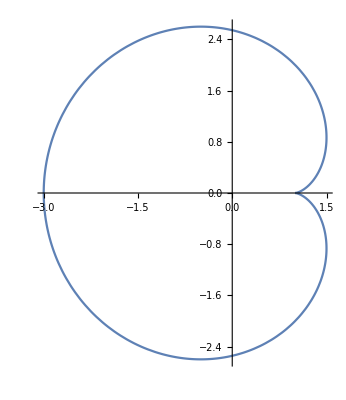

```mathematica
With[{B=1,n=1},
ParametricPlot[{Re[B((n+1)ⅇ^(ⅈ t)-ⅇ^(ⅈ(n+1)t))],Im[B((n+1)ⅇ^(ⅈ t)-ⅇ^(ⅈ(n+1)t))]},{t,0,2π}]]
```

```mathematica
z=B((n+1)ⅇ^(ⅈ t)-ⅇ^(ⅈ(n+1)t))
```

B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))

```mathematica
dz=D[(B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))), t]
```

B (ⅈ ⅇ^(ⅈ t) (1+n)-ⅈ ⅇ^(ⅈ (1+n) t) (1+n))

```mathematica
Conjugate[z]dz
```

B (ⅈ ⅇ^(ⅈ t) (1+n)-ⅈ ⅇ^(ⅈ (1+n) t) (1+n)) Conjugate[B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))]

```mathematica
∫B (ⅈ ⅇ^(ⅈ t) (1+n)-ⅈ ⅇ^(ⅈ (1+n) t) (1+n)) Conjugate[B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))]ⅆt
```

B ∫(ⅈ ⅇ^(ⅈ t) (1+n)-ⅈ ⅇ^(ⅈ (1+n) t) (1+n)) Conjugate[B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))]ⅆt

```mathematica
x[t_]=%
```

B ∫(ⅈ ⅇ^(ⅈ t) (1+n)-ⅈ ⅇ^(ⅈ (1+n) t) (1+n)) Conjugate[B (-ⅇ^(ⅈ (1+n) t)+ⅇ^(ⅈ t) (1+n))]ⅆt

```mathematica
Clear[z]
1/(q-p)∫_p^q zⅆz
```

(-p^2/2+q^2/2)/(-p+q)

```mathematica
Simplify[(-p^2/2+q^2/2)/(-p+q)]
```

(p+q)/2

```mathematica
1/(q-p)∫_p^q z^2 ⅆz
Simplify[%]
```

(-p^3/3+q^3/3)/(-p+q)

1/3 (p^2+p q+q^2)